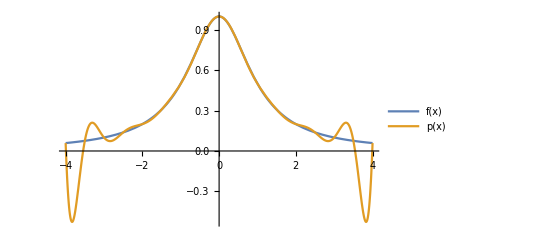

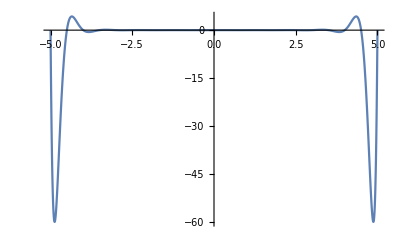

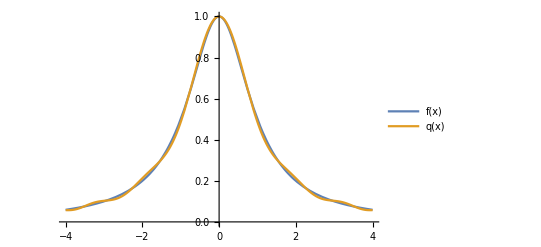

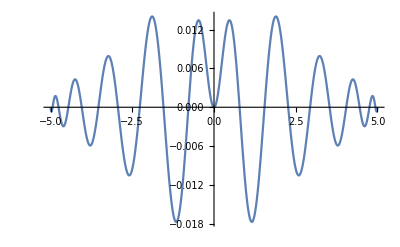

```mathematica
f[x_]:=(x^2+1)^(-1)
px =Array[#&,21,{-5,5}];(*equal length*)
px2= Table[N[5Cos[i π/20]],{i,0,20}]; (*Chebyshev*)
(*My Lagrange function, not using InterpolatingPolynomial*)
l[px_]:=Sum[Product[If[j≠i,x-px[[j]]],{j,1,21}]/Product[If[j≠i,px[[i]]-px[[j]]],{j,1,21}] f[px[[i]]],{i,1,21}];
Plot[{Legended[f[x],"f(x)"],Legended[l[px],"p(x)"]},{x,-4,4}]
Plot[l[px]-f[x],{x,-5,5},PlotRange->Full]
Plot[{Legended[f[x],"f(x)"],Legended[l[px2],"q(x)"]},{x,-4,4}]
Plot[l[px2]-f[x],{x,-5,5}]
```